## Page-Wootters model: NN-level clock + 2-level system

```mathematica
NN= 32
```

32

```mathematica
T := DiagonalMatrix[Range[0,NN-1]] * π / 16
```

```mathematica
MatrixForm[T]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | π/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | π/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (3 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (5 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (3 π)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (7 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (9 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (5 π)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (11 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 π)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (13 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (7 π)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (15 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (17 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (9 π)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (19 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (5 π)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (21 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (11 π)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (23 π)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 π)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (25 π)/16 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (13 π)/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (27 π)/16 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (7 π)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (29 π)/16 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (15 π)/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (31 π)/16)

```mathematica
F := FourierMatrix[NN]
```

```mathematica
Ω := F.T.F† * 16 / π
```

```mathematica
Ω[[1]][[2]]
```

(16 ((-1/32+ⅈ/32) π+1/512 ⅇ^(-(ⅈ π)/16) π+31/512 ⅇ^((ⅈ π)/16) π+1/256 ⅇ^(-(ⅈ π)/8) π+15/256 ⅇ^((ⅈ π)/8) π+3/512 ⅇ^(-(3 ⅈ π)/16) π+29/512 ⅇ^((3 ⅈ π)/16) π+1/128 ⅇ^(-(ⅈ π)/4) π+7/128 ⅇ^((ⅈ π)/4) π+5/512 ⅇ^(-(5 ⅈ π)/16) π+27/512 ⅇ^((5 ⅈ π)/16) π+3/256 ⅇ^(-(3 ⅈ π)/8) π+13/256 ⅇ^((3 ⅈ π)/8) π+7/512 ⅇ^(-(7 ⅈ π)/16) π+25/512 ⅇ^((7 ⅈ π)/16) π+9/512 ⅇ^(-(9 ⅈ π)/16) π+23/512 ⅇ^((9 ⅈ π)/16) π+5/256 ⅇ^(-(5 ⅈ π)/8) π+11/256 ⅇ^((5 ⅈ π)/8) π+11/512 ⅇ^(-(11 ⅈ π)/16) π+21/512 ⅇ^((11 ⅈ π)/16) π+3/128 ⅇ^(-(3 ⅈ π)/4) π+5/128 ⅇ^((3 ⅈ π)/4) π+13/512 ⅇ^(-(13 ⅈ π)/16) π+19/512 ⅇ^((13 ⅈ π)/16) π+7/256 ⅇ^(-(7 ⅈ π)/8) π+9/256 ⅇ^((7 ⅈ π)/8) π+15/512 ⅇ^(-(15 ⅈ π)/16) π+17/512 ⅇ^((15 ⅈ π)/16) π))/π

```mathematica
Ω[[1]][[2]] // Simplify
```

(1/2+ⅈ/2) (-1)^(1/16) (1+(-1)^(1/16)+(-1)^(1/8)+(-1)^(3/16)+(-1)^(1/4)+(-1)^(5/16)+(-1)^(3/8)+(-1)^(7/16))

Hamiltonian in "ordinary" space

```mathematica
Hs := ⅈ{{0,1},{-1,0}}
```

```mathematica
MatrixForm[Hs]
```

(0 | ⅈ
-ⅈ | 0)

```mathematica
TeXForm[Hs]
```

"\\left(\n\\begin{array}{cc}\n 0 & i \\\\\n -i & 0 \\\\\n\\end{array}\n\\right)"

Matrix representation of eq. (1) in https://arxiv.org/abs/1504.04215 by Lloyd, Giovannetti and Maccone.
We turn it into numeric as treating  it symbolically onwards would be unfeasible.

```mathematica
J := N[KroneckerProduct[Ω,IdentityMatrix[2]] + KroneckerProduct[IdentityMatrix[NN],Hs]]
```

```mathematica
Chop[Eigenvalues[J]]
```

{32.,31.,30.,30.,29.,29.,28.,28.,27.,27.,26.,26.,25.,25.,24.,24.,23.,23.,22.,22.,21.,21.,20.,20.,19.,19.,18.,18.,17.,17.,16.,16.,15.,15.,14.,14.,13.,13.,12.,12.,11.,11.,10.,10.,9.,9.,8.,8.,7.,7.,6.,6.,5.,5.,4.,4.,3.,3.,2.,2.,1.,1.,-1.,0}

```mathematica
Chop[Eigensystem[J]]
```

{{32.,31.,30.,30.,29.,29.,28.,28.,27.,47,3.,3.,2.,2.,1.,1.,-1.,0},{1}}
 |  |  |  |

```mathematica
Eigenvalues[J][[40]]
```

12.

```mathematica
Eigenvalues[J][[41]]
```

11.

```mathematica
chosenEigenvector := Eigenvectors[J][[ 40]]

chosenEigenvectorB := Eigenvectors[J][[41]]
```

```mathematica
Normalization := Sqrt[Abs[chosenEigenvector[[1]]^2] + Abs[chosenEigenvector[[2]]^2] ]
```

```mathematica
NormalizationB := Sqrt[Abs[chosenEigenvectorB[[1]]^2] + Abs[chosenEigenvectorB[[2]]^2] ]

chosenEigenvectorNormalized  := chosenEigenvector / Normalization
```

```mathematica
chosenEigenvectorNormalizedB  = chosenEigenvectorB / NormalizationB
```

{0.891003-0.00706481 ⅈ,0.116809-0.438657 ⅈ,-0.421247+0.796948 ⅈ,0.3895+0.188982 ⅈ,-0.493242-0.735079 ⅈ,-0.282733+0.369369 ⅈ,0.838946-0.0875918 ⅈ,-0.319857-0.431497 ⅈ,-0.281045+0.726767 ⅈ,0.602893-0.171301 ⅈ,-0.477092-0.508839 ⅈ,-0.10139+0.709357 ⅈ,0.570843-0.205132 ⅈ,-0.657478-0.446969 ⅈ,1.09906×10^-15+0.519089 ⅈ,0.751354-0.407449 ⅈ,-0.438657-0.116809 ⅈ,0.00706481+0.891003 ⅈ,0.188982-0.3895 ⅈ,-0.796948-0.421247 ⅈ,0.369369+0.282733 ⅈ,0.735079-0.493242 ⅈ,-0.431497+0.319857 ⅈ,0.0875918+0.838946 ⅈ,-0.171301-0.602893 ⅈ,-0.726767-0.281045 ⅈ,0.709357+0.10139 ⅈ,0.508839-0.477092 ⅈ,-0.446969+0.657478 ⅈ,0.205132+0.570843 ⅈ,-0.407449-0.751354 ⅈ,-0.519089+1.09906×10^-15 ⅈ,0.891003-0.00706481 ⅈ,0.116809-0.438657 ⅈ,-0.421247+0.796948 ⅈ,0.3895+0.188982 ⅈ,-0.493242-0.735079 ⅈ,-0.282733+0.369369 ⅈ,0.838946-0.0875918 ⅈ,-0.319857-0.431497 ⅈ,-0.281045+0.726767 ⅈ,0.602893-0.171301 ⅈ,-0.477092-0.508839 ⅈ,-0.10139+0.709357 ⅈ,0.570843-0.205132 ⅈ,-0.657478-0.446969 ⅈ,2.27663×10^-15+0.519089 ⅈ,0.751354-0.407449 ⅈ,-0.438657-0.116809 ⅈ,0.00706481+0.891003 ⅈ,0.188982-0.3895 ⅈ,-0.796948-0.421247 ⅈ,0.369369+0.282733 ⅈ,0.735079-0.493242 ⅈ,-0.431497+0.319857 ⅈ,0.0875918+0.838946 ⅈ,-0.171301-0.602893 ⅈ,-0.726767-0.281045 ⅈ,0.709357+0.10139 ⅈ,0.508839-0.477092 ⅈ,-0.446969+0.657478 ⅈ,0.205132+0.570843 ⅈ,-0.407449-0.751354 ⅈ,-0.519089+0. ⅈ}

```mathematica
probability := Abs[chosenEigenvectorNormalized ^2]
```

```mathematica
probabilityB := Abs[chosenEigenvectorNormalizedB^2]
```

```mathematica
probability
```

{0.813057,0.186943,0.686489,0.313511,0.531529,0.468471,0.371769,0.628231,0.231532,0.768468,0.132166,0.867834,0.0887995,0.9112,0.108035,0.891965,0.186943,0.813057,0.313511,0.686489,0.468471,0.531529,0.628231,0.371769,0.768468,0.231532,0.867834,0.132166,0.9112,0.0887995,0.891965,0.108035,0.813057,0.186943,0.686489,0.313511,0.531529,0.468471,0.371769,0.628231,0.231532,0.768468,0.132166,0.867834,0.0887995,0.9112,0.108035,0.891965,0.186943,0.813057,0.313511,0.686489,0.468471,0.531529,0.628231,0.371769,0.768468,0.231532,0.867834,0.132166,0.9112,0.0887995,0.891965,0.108035}

```mathematica
probabilityB
```

{0.793936,0.206064,0.812576,0.187424,0.783629,0.216371,0.711502,0.288498,0.607176,0.392824,0.486533,0.513467,0.367941,0.632059,0.269453,0.730547,0.206064,0.793936,0.187424,0.812576,0.216371,0.783629,0.288498,0.711502,0.392824,0.607176,0.513467,0.486533,0.632059,0.367941,0.730547,0.269453,0.793936,0.206064,0.812576,0.187424,0.783629,0.216371,0.711502,0.288498,0.607176,0.392824,0.486533,0.513467,0.367941,0.632059,0.269453,0.730547,0.206064,0.793936,0.187424,0.812576,0.216371,0.783629,0.288498,0.711502,0.392824,0.607176,0.513467,0.486533,0.632059,0.367941,0.730547,0.269453}

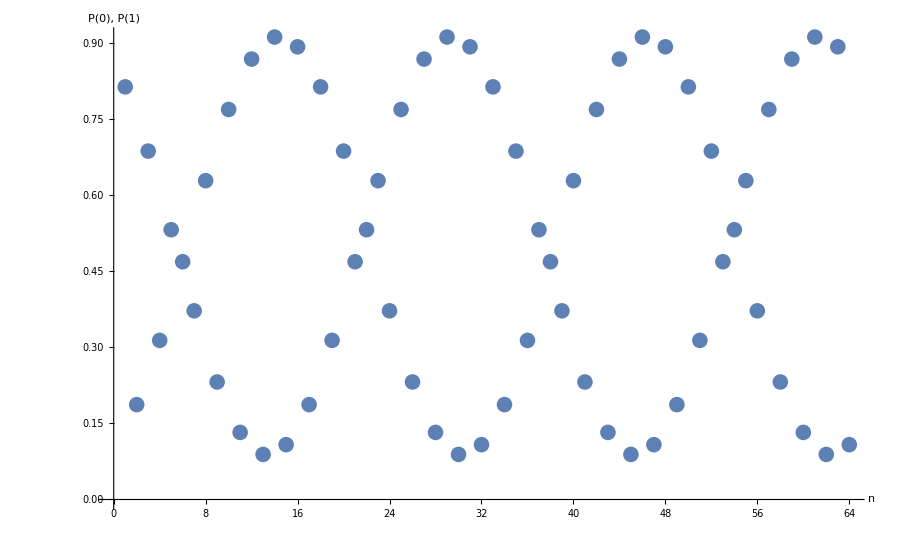

```mathematica
ListPlot[probability,
GridLines->{Range[0,NN*2, 2], Range[0,1,0.1]}, 
AxesLabel->{n, "P(0), P(1)"},
LabelStyle->Directive[16],
PlotMarkers->{Automatic,16},
ImageSize->900
]
```

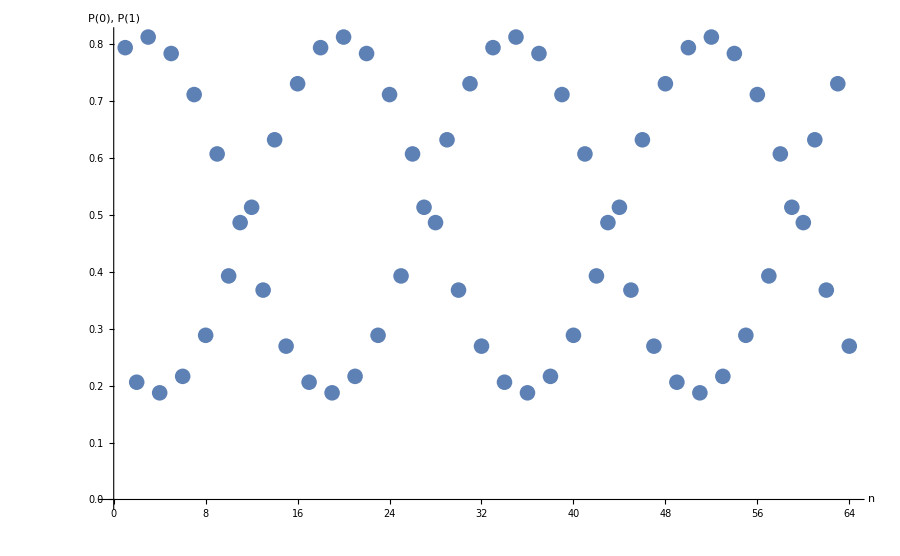

```mathematica
ListPlot[probabilityB, 
GridLines ->{Range[0,NN*2, 2], Range[0,1,0.1]},
AxesLabel->{n, "P(0), P(1)"},
LabelStyle->Directive[16],
PlotMarkers->{Automatic,16},
ImageSize->900
]
```

Consistency of PW with ordinary QM (discrete approximation):

```mathematica
chosenEigenvectorNormalizedB
```

{0.891003-0.00706481 ⅈ,0.116809-0.438657 ⅈ,-0.421247+0.796948 ⅈ,0.3895+0.188982 ⅈ,-0.493242-0.735079 ⅈ,-0.282733+0.369369 ⅈ,0.838946-0.0875918 ⅈ,-0.319857-0.431497 ⅈ,-0.281045+0.726767 ⅈ,0.602893-0.171301 ⅈ,-0.477092-0.508839 ⅈ,-0.10139+0.709357 ⅈ,0.570843-0.205132 ⅈ,-0.657478-0.446969 ⅈ,1.09906×10^-15+0.519089 ⅈ,0.751354-0.407449 ⅈ,-0.438657-0.116809 ⅈ,0.00706481+0.891003 ⅈ,0.188982-0.3895 ⅈ,-0.796948-0.421247 ⅈ,0.369369+0.282733 ⅈ,0.735079-0.493242 ⅈ,-0.431497+0.319857 ⅈ,0.0875918+0.838946 ⅈ,-0.171301-0.602893 ⅈ,-0.726767-0.281045 ⅈ,0.709357+0.10139 ⅈ,0.508839-0.477092 ⅈ,-0.446969+0.657478 ⅈ,0.205132+0.570843 ⅈ,-0.407449-0.751354 ⅈ,-0.519089+1.09906×10^-15 ⅈ,0.891003-0.00706481 ⅈ,0.116809-0.438657 ⅈ,-0.421247+0.796948 ⅈ,0.3895+0.188982 ⅈ,-0.493242-0.735079 ⅈ,-0.282733+0.369369 ⅈ,0.838946-0.0875918 ⅈ,-0.319857-0.431497 ⅈ,-0.281045+0.726767 ⅈ,0.602893-0.171301 ⅈ,-0.477092-0.508839 ⅈ,-0.10139+0.709357 ⅈ,0.570843-0.205132 ⅈ,-0.657478-0.446969 ⅈ,2.27663×10^-15+0.519089 ⅈ,0.751354-0.407449 ⅈ,-0.438657-0.116809 ⅈ,0.00706481+0.891003 ⅈ,0.188982-0.3895 ⅈ,-0.796948-0.421247 ⅈ,0.369369+0.282733 ⅈ,0.735079-0.493242 ⅈ,-0.431497+0.319857 ⅈ,0.0875918+0.838946 ⅈ,-0.171301-0.602893 ⅈ,-0.726767-0.281045 ⅈ,0.709357+0.10139 ⅈ,0.508839-0.477092 ⅈ,-0.446969+0.657478 ⅈ,0.205132+0.570843 ⅈ,-0.407449-0.751354 ⅈ,-0.519089+0. ⅈ}

```mathematica
psi0 :=  chosenEigenvectorNormalizedB[[{1,2}]]
```

```mathematica
psi0
```

{0.891003-0.00706481 ⅈ,0.116809-0.438657 ⅈ}

```mathematica
psi[t_] := MatrixExp[-ⅈ Hs t, psi0 ]
```

```mathematica
psi[t]
```

{(0.891003-0.00706481 ⅈ) Cos[t]+(0.116809-0.438657 ⅈ) Sin[t],(0.116809-0.438657 ⅈ) Cos[t]-(0.891003-0.00706481 ⅈ) Sin[t]}

```mathematica
Abs[psi[t]]^2
```

{Abs[(0.891003-0.00706481 ⅈ) Cos[t]+(0.116809-0.438657 ⅈ) Sin[t]]^2,Abs[(0.116809-0.438657 ⅈ) Cos[t]-(0.891003-0.00706481 ⅈ) Sin[t]]^2}

```mathematica
(Abs[psi[t]]^2)[[1]]
```

Abs[(0.891003-0.00706481 ⅈ) Cos[t]+(0.116809-0.438657 ⅈ) Sin[t]]^2

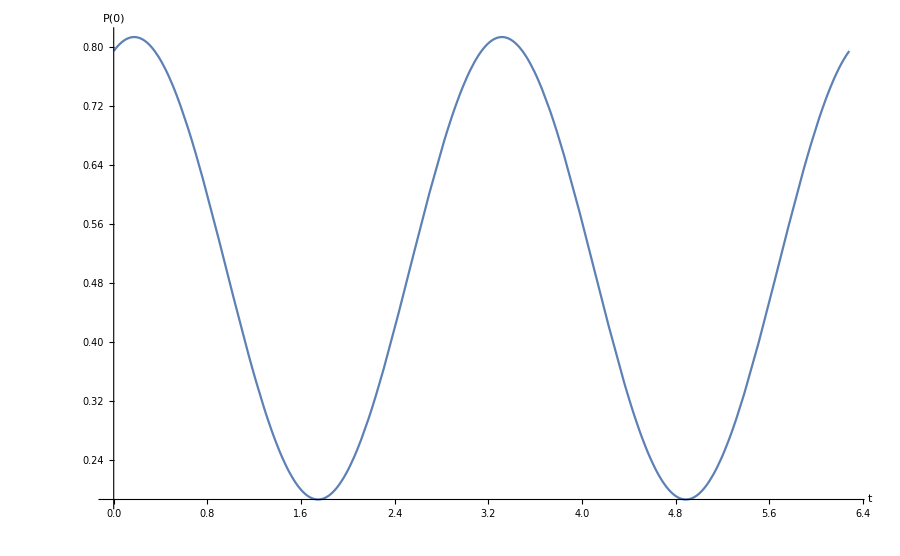

```mathematica
Plot[(Abs[psi[t]]^2)[[1]],{t,0,2π},
AxesLabel->{t, "P(0)"},
LabelStyle->Directive[16],
ImageSize->900
]
```

```mathematica
(Abs[psi[t]]^2)[[2]]
```

Abs[(0.116809-0.438657 ⅈ) Cos[t]-(0.891003-0.00706481 ⅈ) Sin[t]]^2

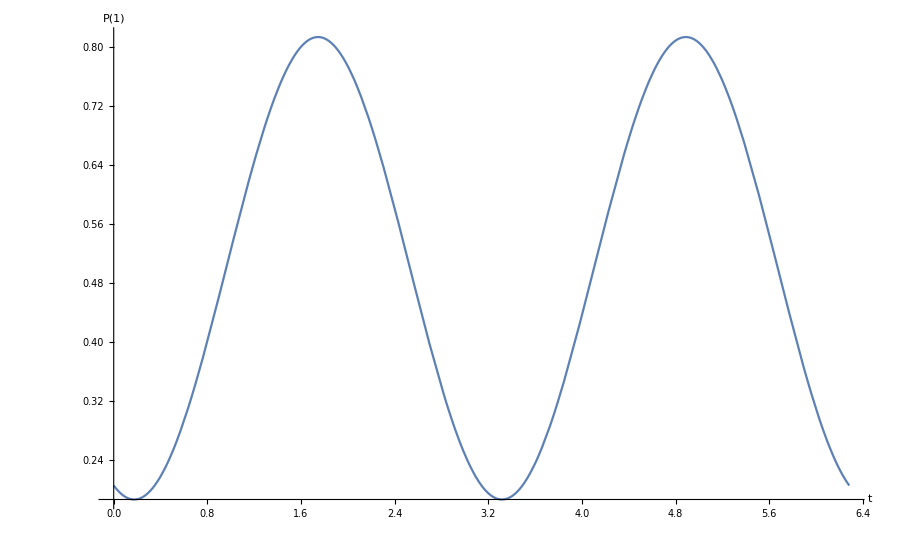

```mathematica
Plot[(Abs[psi[t]]^2)[[2]],{t,0,2π},
AxesLabel->{t, "P(1)"},
LabelStyle->Directive[16],
ImageSize->900
]
```

### Complex evolution of ψ (not just |ψ|^2)

```mathematica
psi[t][[1]] (* <0| *)
```

(0.891003-0.00706481 ⅈ) Cos[t]+(0.116809-0.438657 ⅈ) Sin[t]

```mathematica
psi[t][[2]] (* <1| *)
```

(0.116809-0.438657 ⅈ) Cos[t]-(0.891003-0.00706481 ⅈ) Sin[t]

- please note index count is 1, 2 but refers, respectively, to computational base elements |0>, |1> in ordinary Hilbert space

```mathematica
re0psi[t_] := Simplify[Re[psi[t][[1]]], Assumptions->Element[t, Reals]]
```

```mathematica
im0psi[t_] := Simplify[Im[psi[t][[1]]], Assumptions->Element[t, Reals]]
```

```mathematica
re1psi[t_] := Simplify[Re[psi[t][[2]]], Assumptions->Element[t, Reals]]
```

```mathematica
im1psi[t_] := Simplify[Im[psi[t][[2]]], Assumptions->Element[t, Reals]]
```

```mathematica
zAxis := ParametricPlot3D[{0,0,t}, {t,0,2π}, PlotStyle->{Gray}]
```

```mathematica
psi0plot := ParametricPlot3D[{re0psi[t], im0psi[t], t}, {t, 0, 2π}, PlotStyle->{Red} ]
```

```mathematica
psi1plot := ParametricPlot3D[{re1psi[t], im1psi[t], t}, {t, 0, 2π}, PlotStyle->{Blue} ]
```

```mathematica
Show[zAxis, psi0plot,psi1plot, ImageSize->Medium,
AxesLabel->{Style[Re["<0,1|ψ>"], Bold], Style[Im["<0,1|ψ>"], Bold], Style[t, Bold]}
]
```

-Graphics3D-

```mathematica
pi = N[π]
```

3.14159

```mathematica
rephased[k_] := chosenEigenvectorNormalizedB [[k]] * Exp[-ⅈ*pi*11*(k-1)/NN]
```

```mathematica
rephased1[k_] := chosenEigenvectorNormalizedB [[k]] * Exp[-ⅈ*pi*11*(k-2)/NN]
```

```mathematica
scatter[k_] := {Re[ rephased[k]], Im[ rephased[k]], pi*(k-1)/NN}
```

```mathematica
scatter1[k_] := {Re[ rephased1[k]], Im[ rephased1[k]], pi*(k-2)/NN}
```

```mathematica
scatterPoints = Map[scatter, Range[1,2*NN, 2]]
```

{{0.891003,-0.00706481,0.},{0.896671,-0.0925068,0.19635},{0.86788,-0.174394,0.392699},{0.805737,-0.249579,0.589049},{0.71263,-0.315173,0.785398},{0.592137,-0.368655,0.981748},{0.448889,-0.40797,1.1781},{0.28839,-0.431607,1.37445},{0.116809,-0.438657,1.5708},{-0.0592618,-0.42885,1.76715},{-0.233055,-0.402563,1.9635},{-0.397892,-0.360805,2.15984},{-0.547438,-0.305182,2.35619},{-0.675946,-0.237831,2.55254},{-0.778478,-0.16134,2.74889},{-0.851094,-0.0786487,2.94524},{-0.891003,0.00706481,3.14159},{-0.896671,0.0925068,3.33794},{-0.86788,0.174394,3.53429},{-0.805737,0.249579,3.73064},{-0.71263,0.315173,3.92699},{-0.592137,0.368655,4.12334},{-0.448889,0.40797,4.31969},{-0.28839,0.431607,4.51604},{-0.116809,0.438657,4.71239},{0.0592618,0.42885,4.90874},{0.233055,0.402563,5.10509},{0.397892,0.360805,5.30144},{0.547438,0.305182,5.49779},{0.675946,0.237831,5.69414},{0.778478,0.16134,5.89049},{0.851094,0.0786487,6.08684}}

```mathematica
scatterPoints1 = Map[scatter1, Range[2,2*NN, 2]]
```

{{0.116809,-0.438657,0.},{-0.0592618,-0.42885,0.19635},{-0.233055,-0.402563,0.392699},{-0.397892,-0.360805,0.589049},{-0.547438,-0.305182,0.785398},{-0.675946,-0.237831,0.981748},{-0.778478,-0.16134,1.1781},{-0.851094,-0.0786487,1.37445},{-0.891003,0.00706481,1.5708},{-0.896671,0.0925068,1.76715},{-0.86788,0.174394,1.9635},{-0.805737,0.249579,2.15984},{-0.71263,0.315173,2.35619},{-0.592137,0.368655,2.55254},{-0.448889,0.40797,2.74889},{-0.28839,0.431607,2.94524},{-0.116809,0.438657,3.14159},{0.0592618,0.42885,3.33794},{0.233055,0.402563,3.53429},{0.397892,0.360805,3.73064},{0.547438,0.305182,3.92699},{0.675946,0.237831,4.12334},{0.778478,0.16134,4.31969},{0.851094,0.0786487,4.51604},{0.891003,-0.00706481,4.71239},{0.896671,-0.0925068,4.90874},{0.86788,-0.174394,5.10509},{0.805737,-0.249579,5.30144},{0.71263,-0.315173,5.49779},{0.592137,-0.368655,5.69414},{0.448889,-0.40797,5.89049},{0.28839,-0.431607,6.08684}}

```mathematica
Range[1,2*NN, 2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63}

```mathematica
scatterPlot = ListPointPlot3D[scatterPoints, PlotStyle->{Red, PointSize[Large]}]
```

-Graphics3D-

```mathematica
scatterPlot1 = ListPointPlot3D[scatterPoints1, PlotStyle->{Blue, PointSize[Large]}]
```

-Graphics3D-

```mathematica
Show[zAxis, psi0plot,psi1plot,scatterPlot, scatterPlot1, ImageSize->Large,
AxesLabel->{Style[Re["<0,1|ψ>"], Bold], Style[Im["<0,1|ψ>"], Bold], Style[t, Bold]}
]
```

-Graphics3D-